# Demo: Kitaev Chain

The Kitaev chain is a prototype example of the topological superconductor. Here we demonstrate how to examine its properties using Q3.

FockNumberpaclet:Q3/ref/FockNumberQ3 Package Symbol or Qpaclet:Q3/ref/QQ3 Package Symbol | Number operator
FockHoppingpaclet:Q3/ref/FockHoppingQ3 Package Symbol or Hoppaclet:Q3/ref/HopQ3 Package Symbol | Constructs the hopping Hamiltonian terms
FockPairingpaclet:Q3/ref/FockPairingQ3 Package Symbol or Pairpaclet:Q3/ref/PairQ3 Package Symbol | Constructs the pairing Hamiltonian terms

Some useful functions to study the Kitaev chain.

See Kitaev original paper [A. Kitaev, Physics-Uspekhi 44, 131 (2001)https://doi.org/10.1070/1063-7869/44/10S/S29] for technical details of the model.

Load the Fockpaclet:Q3/guide/QuantumManyBodySystems package.

```mathematica
<<Q3`
```

Let c denote the (Dirac) Fermionpaclet:Q3/ref/FermionQ3 Package Symbol operator.

```mathematica
Let[Fermion,c]
```

Let t, μ, and Δ denote the hopping amplitude, chemical potential, and pairing potential, respectively.

```mathematica
Let[Real,t,μ,Δ]
```

The number of sites of the one-dimensional lattice.

```mathematica
$L=8;
```

Define some Lists of operators to be used later.

```mathematica
cc=c[Range[1,$L]]
cccc=Join[cc,Dagger@cc]
```

{c_1,c_2,c_3,c_4,c_5,c_6,c_7,c_8}

{c_1,c_2,c_3,c_4,c_5,c_6,c_7,c_8,c_1^†,c_2^†,c_3^†,c_4^†,c_5^†,c_6^†,c_7^†,c_8^†}

Now constructs the model Hamiltonian.

```mathematica
H0=-μ*Q[cc]
Hhop=-t*PlusDagger @ FockHopping[cc]
Hpair=-Δ*PlusDagger @ FockPairing[cc]
Htotal=H0+Hhop+Hpair
```

-μ (c_1^†c_1+c_2^†c_2+c_3^†c_3+c_4^†c_4+c_5^†c_5+c_6^†c_6+c_7^†c_7+c_8^†c_8)

-t (c_1^†c_2+c_2^†c_1+c_2^†c_3+c_3^†c_2+c_3^†c_4+c_4^†c_3+c_4^†c_5+c_5^†c_4+c_5^†c_6+c_6^†c_5+c_6^†c_7+c_7^†c_6+c_7^†c_8+c_8^†c_7)

-Δ (-c_2 c_1-c_3 c_2-c_4 c_3-c_5 c_4-c_6 c_5-c_7 c_6-c_8 c_7-c_1^†c_2^†-c_2^†c_3^†-c_3^†c_4^†-c_4^†c_5^†-c_5^†c_6^†-c_6^†c_7^†-c_7^†c_8^†)

-Graphics-

Let us take a look at the connectivity of the model.

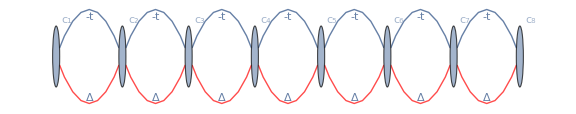

```mathematica
GraphForm[Htotal]
```

Here the black thin lines indicate single-particle tunneling and the red thick lines represent the p-wave pairing.

To investigate the quasi-particle spectrum (by means of the Bogoliubov-de Gennes equation), obtain the single-particle BdG Hamiltonian.

```mathematica
matK=CoefficientTensor[Htotal,Dagger@cccc,cccc];
matK//MatrixForm
```

(-μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | 0
-t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0
0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | 0
0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | 0
0 | 0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0
0 | 0 | 0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2 | 0
0 | 0 | 0 | 0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | Δ/2
0 | 0 | 0 | 0 | 0 | 0 | -t/2 | -μ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0
0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | μ/2 | t/2 | 0 | 0 | 0 | 0 | 0 | 0
Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0 | 0 | 0 | 0
0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0 | 0 | 0
0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0 | 0
0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0
0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2 | 0
0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2 | t/2
0 | 0 | 0 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t/2 | μ/2)

Now study the quasi-particle energy spectrum of the model. (Be aware of the finite size effects.)

```mathematica
KK[μ_,t_,Δ_]=matK;
Manipulate[
Module[
{eval=Table[Sort@Eigenvalues[KK[μ,1.,Δ]],{μ,0,5,0.05}]},
ListLinePlot[Transpose@eval,
Axes->None,
Frame->True,
FrameLabel->{"μ / t","Eenergy / t"},
DataRange->{0,5}]
],
{{Δ,1},0,2,0.1}
]
```

## References

A. Kitaev, Physics-Uspekhi 44, 131 (2001)https://doi.org/10.1070/1063-7869/44/10S/S29

| Related Guides
▪Quantum Many-Body Systems

| Related Tutorials
▪Quantum Many-Body Systems
▪Q3: Quick Start

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/